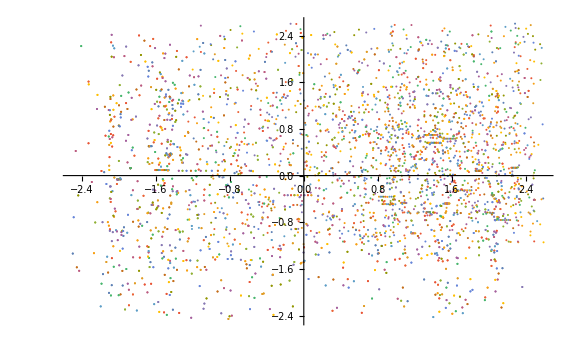

```mathematica
Clear["Global'*"]
arxikes=Table[{x0,y0},{x0,1.67,1.69,0.002},{y0,0,0.02,0.002}];
data=Block[{a=0.15},Reap[For[i=1,i<=9,i++,
x0=arxikes[[i,1]]; y0=arxikes[[i,2]];
NDSolve[{x''[t]-x[t]+x[t]^3-x[t]^2==a*Cos[t],x[0]==x0,x'[0]==y0
,WhenEvent[Mod[t,2 π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,1000}]]]][[-1,1]];
lpd=ListPlot[data, ImageSize -> Large, PlotRange -> Full, PlotStyle -> PointSize[0.0025]]
```

```mathematica
Clear[Data]
```

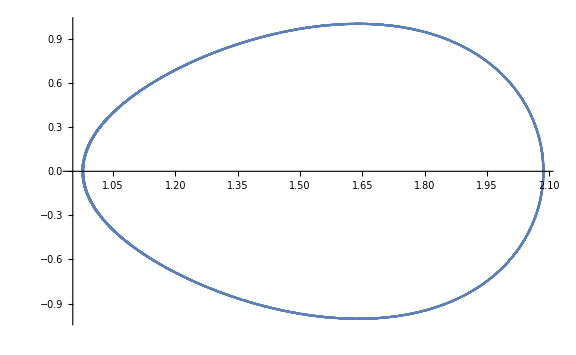

```mathematica
data=Block[{a=0.15},Reap[NDSolve[{x''[t]-x[t]+x[t]^3-x[t]^2==a Cos[t],x[0]==1.69,x'[0]==-1
,WhenEvent[Mod[t,2 π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,100000},MaxSteps->∞]]][[-1,1]];
lpd=ListPlot[data, ImageSize -> Large, PlotRange -> Full, PlotStyle -> PointSize[0.0025]]
```

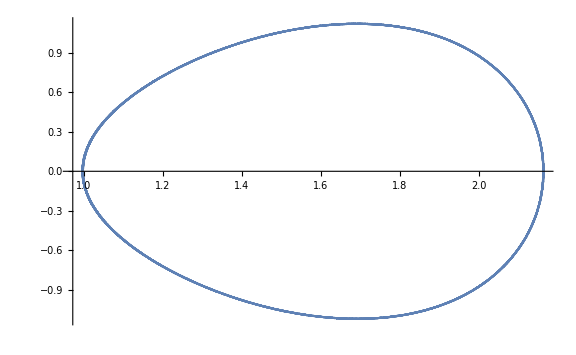

```mathematica
data=Block[{a=0.15},Reap[NDSolve[{x''[t]-x[t]+x[t]^3-x[t]^2==a Cos[t],x[0]==1,x'[0]==-0.1
,WhenEvent[Mod[t,2 π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,100000},MaxSteps->∞]]][[-1,1]];
lpd=ListPlot[data, ImageSize -> Large, PlotRange -> Full, PlotStyle -> PointSize[0.0025]]
```